# Backwards Differentiation Formulas

As always a reminder our target is to be able to understand literature such as https://en.wikipedia.org/wiki/Backward_differentiation_formula.  Of course, our real target is more involved professional literature but the Wiki page is a start.

## Example Stiff Problem

We are going to start with a simple test problem
	y'=A.y
where A is the matrix from approximating u_xx using standard centered differences.   See Rabeya’s talk for details.  For reasonable n matrix has some large negative eigenvalues!  This means that there are some bits of the solution that decay very rapidly.   This is bad news because the ODE solvers you learnt in Calculus One will need to take tiny steps. We need solvers that can take reasonable sized steps in circumstances where there are rapidly decaying components of the solution!

```mathematica
m=100;
A=(m+1)^2 SparseArray[{
Band[{1,1}]->-2,
Band[{1,2}]->1,
Band[{2,1}]->1},{m,m}];
ListPlot[Eigenvalues[A]]
```

For Rabeya’s test problem we should be able to explicitly compare the matrix exponential 
	ⅇ^(A t)y_0	
solution to whatever we get from our approximations.    The large negative eigenvalues (indicating fast time scales for decay) in the same problem as slower time scales.

## Explicit Euler

The Explicit Euler approximation with a fixed step size h for 
	y'(t)=f(t,y(t))  with y(0)=y_0
is simply
	y_(k+1)=y_k+h f(k h,y_k).
For Rabeya’s test problem y'=A.y we get
	y_1=y_0+h A.y_0
organizing and repeating the process gives
	y_1 | = | (I+h A).y_0
y_2 | = | (I+h A)^2.y_0
  | ⋮ |  
y_k | = | (I+h A)^k.y_0

The question is when does this look like the matrix exponential?

## Implicit Euler

The Implicit Euler approximation aka BDF_1 with a fixed step size h for 
	y'(t)=f(t,y(t))  with y(0)=y_0
is simply
	y_(k+1)=y_k+h f((k+1) h,y_(k+1)).
For Rabeya’s test problem y'=A.y we we get
	y_1=y_0+h A.y_1
or equivalently
	y_1=(I-h A)^-1.y_0
organizing and repeating the process gives
	y_1 | = | (I-h A)^-1.y_0
y_2 | = | (I-h A)^-2.y_0
  | ⋮ |  
y_k | = | (I-h A)^-k.y_0

The question is when does this look like the matrix exponential?

## Mid Point aka Crank-Nicolson

A trapezoid approximation with a fixed step size h for 
	y'(t)=f(t,y(t))  with y(0)=y_0
is called the Crank-Nicolson scheme in PDE problems.
	y_(k+1)=y_k+h/2 (f(k h,y_k)+f((k+1) h, y_(k+1))).
For Rabeya’s test problem y'=A.y we we get
	y_1=y_0+h/2 (A.y_0+A.y_1)
or equivalently
	y_1=(I-h/2 A)^-1.(I+h/2 A).y_0
organizing and repeating the process gives
	y_1 | = | ((I-h/2 A)^-1.(I+h/2 A))^1.y_0
y_2 | = | ((I-h/2 A)^-1.(I+h/2 A))^2.y_0
  | ⋮ |  
y_k | = | ((I-h/2 A)^-1.(I+h/2 A))^k.y_0
The question is when does this look like the matrix exponential?

## BDF_2

The BDF_1 (aka Implicit Euler) update formula is  
	(y_(k+1)-y_k)/h= h f(t_(k+1),y_(k+1))
The left hand side is just a backwards difference approximation to the derivative.  If we use a slightly fancier approximation to the derivative we get the second of the BDF formula.
	(y_(k+2)-4/3 y_(k+1)+1/3 y_k)/(2/3 h)= h f(t_(k+2),y_(k+2)).  
It may well not be obvious that the left hand side is an approximation to the derivative at some appropriate point.

```mathematica
f[t_]:=t+ ArcTan[t+t^2+Cos[Sin[t]]]
h=0.1;
TabView[{
"BDF_1"->Plot[{f'[t],(f[t+h]-f[t])/h},{t, 0,3}],
"BDF_2"->Plot[{f'[t],(f[t+2h]-4/3 f[t+h]+1/3 f[t])/(2/3 h)},{t, 0,3}],
"BDF_3"->Plot[{f'[t],(f[t+3h]-18/11 f[t+2h]+9/11 f[t+h]-2/11 f[t])/(6/11 h)},{t, 0,3}]
}]
```

123

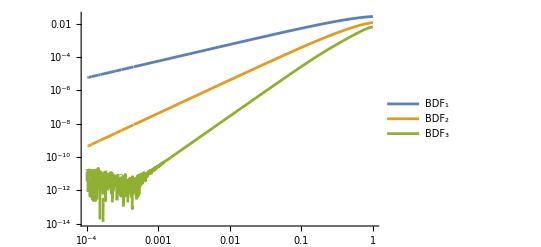

```mathematica
t0=2.1;
LogLogPlot[{
Abs[(f[t0+h]-f[t0])/h-f'[t0+h]],
Abs[(f[t0+2h]-4/3 f[t0+h]+1/3 f[t0])/(2/3 h)-f'[t0+2h]],
Abs[(f[t0+3h]-18/11 f[t0+2h]+9/11 f[t0+h]-2/11 f[t0])/(6/11 h)-f'[t0+3h]]
},{h, 10^-4,1},
PlotLegends->{"BDF_1","BDF_2","BDF_3","h^3"}]
```